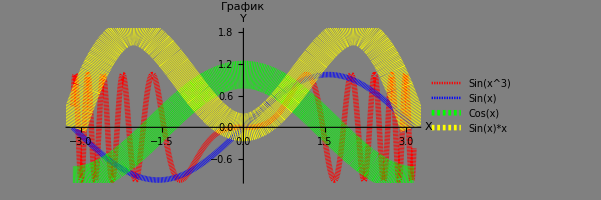

```mathematica
q = Plot[{Sin[x^3], Sin[x],Cos[x], Sin[x]*x},{x, -Pi,Pi},
PlotLabel->"График", AxesLabel->{"X", "Y"},
PlotStyle-> {
{RGBColor[1,0,0], Thickness[0.01],Dashing[0,1,0.005]},
{RGBColor[0,0,1], Thickness[0.01],Dashing[0,1,0.015]},
{RGBColor[0,1,0], Thickness[0.05],Dashing[0,1,0.015]},
{RGBColor[1,1,0], Thickness[0.05],Dashing[0,1,0.015]}
},
Background->RGBColor[0.5,0.5,0.5],
AxesStyle-> {
{RGBColor[1,0,0], Thickness[0.0021]},
{RGBColor[1,0,1], Thickness[0.0015]}
},
AspectRatio->Automatic,
PlotLegends->{"Sin(x^3)","Sin(x)","Cos(x)", "Sin(x)*x"}]
```